# Turing patterns in 1D

#### Solving a RD system in a linear domain with Newman boundary conditions and random initial conditions

The system:

(∂u)/(∂t)= d (∂^2 u)/(∂x)  + F[u,v],
(∂v)/(∂t)=  (∂^2 v)/(∂x)  + G[u,v]

### Chemical kinetics:

#### BVAM

```mathematica
parameters={η-> 1,h->-1,c->1,a -> 3/2,b-> -0.95, d->0.1};
```

```mathematica
F[t,x]=η (u[t, x]+a v[t, x]- c u[t, x] v[t, x]-v[t, x]^2  u[t, x]) /. parameters;
G[t,x]=η (b v[t, x]+ h u[t, x]+c u[t, x] v[t, x]+ v[t, x]^2  u[t, x]) /. parameters;
```

```mathematica
eqpts=Solve[{F[t,x]==0,G[t,x]==0},{u[t,x],v[t,x]}]//Flatten;
{u0,v0}={u[t,x],v[t,x]}/.eqpts
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.,0.}

#### Van der Pol

```mathematica
parameters={μ->1, d->0.025};
```

```mathematica
F[t,x]= v[t, x]+ μ (u[t, x]-u[t, x]^3/3) ;
G[t,x]= -u[t, x];
```

```mathematica
eqpts=Solve[{F[t,x]==0,G[t,x]==0},{u[t,x],v[t,x]}]//Flatten;
{u0,v0}={u[t,x],v[t,x]}/.eqpts;
```

#### Briggs-Rauschen

```mathematica
parameters={ κ->10,μ->6, l->37/27, τ->0.18, d->0.18};
```

```mathematica
F[t,x]= -u[t,x]^3+μ u[t,x] - κ v[t,x] - l /.parameters;
G[t,x]= 1/τ(u[t, x]-v[t,x]) /.parameters;
```

```mathematica
eqpts=Solve[{F[t,x]==0,G[t,x]==0},{u[t,x],v[t,x]}];
{u0,v0}={u[t,x],v[t,x]}/.eqpts[[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

#### Domain and time

```mathematica
L= 10; (* Domain size *)
T=10000; (* End time *)
```

#### The system

```mathematica
eqn = {
Derivative[1,0][u][t, x] == d  Derivative[0,2][u][t, x] +F[t,x] 
+   NeumannValue[0,{x ==0||x==L}],     
Derivative[1,0][v][t, x] == Derivative[0,2][v][t, x] +G[t,x]
+ NeumannValue[0,{x ==0||x==L}]
    } /. parameters;
```

#### Random initial conditions

```mathematica
n=100;  (*Number of points for the initial condition*)
initAmp=0.1; (* Amplitude of the random signal *)
xPoints=Subdivide[0,L,n-1];
uPoints= u0+initAmp*RandomReal[{-0.5,0.5},n];
initialConditionU=Interpolation[Transpose[{xPoints,uPoints}]];
vPoints=v0+initAmp*RandomReal[{-0.5,0.5},n];
initialConditionV=Interpolation[Transpose[{xPoints,vPoints}]];

ics = {u[0,x]==initialConditionU[x],v[0,x]==initialConditionV[x]};
```

#### Solving the equation (0<x<L, 0<t<T). FEM method with a mesh size of 2.5

```mathematica
SystemOptions["FiniteElementOptions"]
```

{FiniteElementOptions→{CacheInterpolationElements→True,DefaultBounds→{-1,1},DefaultElementMeshOrder→2,DefaultExtrapolationHandler→{Indeterminate&,WarningMessage→True},DefaultNumberOfElements→20,DiscontinuousInterpolationTolerance→1.×10^-10,InterpolationToleranceFactor→0.0001,MinimumElementMeshQuality→0.,Parser→Automatic,SymbolicProcessing→1.}}

```mathematica
{ufun,vfun}=NDSolveValue[{eqn,ics},{u,v},x∈Interval[{0,L}],{t,0,T},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.05}}}}];
```

#### Plotting the solution:

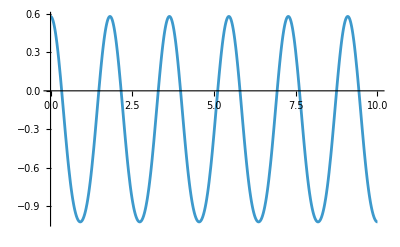

```mathematica
Plot[ufun[T,x],{x,0,L}]
```

Pattern evolution through time:

```mathematica
timeF=250;
uplot=Table[Table[{x,t,ufun[t,x]},{x,0,L,0.1}],{t,0,timeF,1}];
```

```mathematica
Animate[ListPlot3D[uplot[[1;;i]],AxesLabel->{"x","time","u(x,t)"},PlotLabel->Row[{"u(x,t)"}],PlotRange->{{0,L},{0,timeF},{-1.5,0.75}},DataRange->All,PerformanceGoal->"Quality",Mesh->None],{i,2,Length[uplot],1}, AnimationRunning->False, AnimationRepetitions->1]
```